```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run"];
co={"../InputData/Coo100m01_100.txt","../InputData/Coo100m01_500.txt","../InputData/Coo100m01.txt","../InputData/Coo100m005.txt"};
(*al1 22.4 1608662 /Max[tot[[365;;453,2]]]
al0 22.4 1608662 /Max[tot[[365;;453,2]]]*)


Do[pa=Flatten[{numruns=1,maxT=29 365(*must not exceed 10585*),NumPat={100,500,53131,75736}[[i]],muJ=0.05,muA=0.125,beta=100,theta=9,meanTL=0.0667,mindev=10,gamma=(1-0.95)/2,xiA=0.5,eA=0.95,drivertime=270 365+150,NumDriver=1000,NumDriverPat={1,1,10,20}[[i]],d=0.005,Ld=10/110.,psi=0,muAES=0.9,thide1=300,thide2=350,twake1=140,twake2=170,al0=100,al0var=0.,al1=3700,amp=0,resp=1,recstart=10,recend=10000,recIntGlob=1,recIntLoc=365,recsitesfreq=1,set=i,"e","r",start=27 365+1,co[[i]],"../InputData/RainDailyAvAv.csv","none","../InputData/arab_mortality_Jan25.csv"}];
Export["PP"<>ToString[set]<>".csv",pa,"CSV","TextDelimiters"->""],{i,4}];
```

```mathematica
25 365
```

9125

```mathematica
10585/365
```

29

```mathematica
start
```

8761

```mathematica
res=Import["!./gdsimsapp<PP1.csv","Table"];
```

```mathematica
SetDirectory["~/Dropbox/FieldTrials/CRT/CRTModel/Run/output_files"];
tot=Drop[Import["Totals4run1.txt","Table"],2];
Dimensions[tot]
```

{730,7}

```mathematica
Coo=Import["../InputData/Coo100m005.txt","Table"];
Dimensions[Coo]
```

{75736,6}

```mathematica
Coo[[1]]
```

{-4.81204,12.1054,0.0757576,49.6125,0,28}

```mathematica
FracHouet=N[(Length[Coo]-Count[Coo[[All,5]],0])/Length[Coo]];
MaxHouet=FracHouet Max[tot[[365;;730,2]]];
(*NumMos = estimate of max num of mosquitoes - estimated mos per human * estimated num humans*)
NumMos=21 1608662
```

33781902

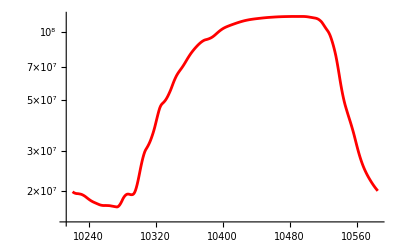

33781902

```mathematica
ListLogPlot[Table[tot[[366;;730,{1,i}]],{i,2,7,1}],PlotStyle->{Red,Blue,Green,Yellow,Orange,Purple},PlotRange->All,Joined->True]
```

```mathematica
Max[tot[[365;;730,2]]]
```

116583440

3687.32

184.366